# Two-outcome experiments on incentivizing honest performative predictions with proper scoring rules

## Caspar Oesterheld*, Johannes Treutlein*, Emery Cooper, and Rubi Hudson

Definitions of scoring rules

Log scoring rule

```mathematica
logscore[0,0]:=0; logscore[1,1]:=0;
logscore[p_,q_]:=q*Log[p]+(1-q)*Log[1-p]
```

Tests

```mathematica
-0.23<=logscore[0.8,1]<=-0.21
```

True

```mathematica
logscore[1,1]==0
```

True

```mathematica
logscore[0,0]==0
```

True

```mathematica
logscore[0,0.001]==-∞
```

True

```mathematica
Last @Last@Last@Maximize[logscore[p,1/3],p]==1/3
```

True

Brier scoring rule

```mathematica
brierscore[p_,q_]:=q*(2*p-p^2-(1-p)^2)+(1-q)*(2*(1-p)-p^2-(1-p)^2)
```

Test

```mathematica
Last@Last@Last@Maximize[brierscore[p,1/5],p]==1/5
```

True

Exponential Scoring rule

```mathematica
exponentialscore[K_,p_,q_]:=Exp[K*p]/K+Exp[K*p](q-p)
```

Test

```mathematica
Last@Last@Last@Maximize[exponentialscore[1/3,p,1/5],p]==1/5
```

True

Linear world functions

```mathematica
f[p_,fp_,slope_]:=(p-fp)*slope+fp
```

Tests

```mathematica
f[0.1,0.5,0.5]==0.3
```

True

```mathematica
f[fp,fp,slope]==fp
```

True

Optimal report functions

```mathematica
Clear[ArgmaxScore];ArgmaxScore[fp_,slope_,S_]:=ArgmaxScore[fp,slope,S]=Last@Last@Last@Maximize[{S[p,f[p,fp,slope]],{p>=0,p<=1}},{p},Method->{"RandomSearch","SearchPoints"->500}]
```

Tests

```mathematica
Abs[ArgmaxScore[1/2,1/3,brierscore]-0.5]<=0.00001
```

Abs[-0.5+(SearchPoints→100)]≤0.00001

```mathematica
Abs[ArgmaxScore[1/2,1/3,logscore]-0.5]<0.00001
```

Abs[-0.5+(SearchPoints→100)]<0.00001

Measures of distance between probabilities

```mathematica
AbsLogOddsRatio[0,0]=0;
AbsLogOddsRatio[1,1]=0;
AbsLogOddsRatio[0,q_]=Infinity;
AbsLogOddsRatio[p_,0]=Infinity;
AbsLogOddsRatio[1,q_]=Infinity;
AbsLogOddsRatio[p_,1]=Infinity;
AbsLogOddsRatio[p_,q_]:=Abs[Log[p]-Log[q]+Log[1-q]-Log[1-p]];
```

```mathematica
L1Distance[p_,q_]:=Abs[p-q]
```

```mathematica
L2DistanceVect[p_,q_]:=√2 Abs[p-q]
```

Tests

```mathematica
Simplify[Norm[{p,1-p}-{q,1-q}]==L2DistanceVect[p,q]]
```

True

Defining the accuracy bounds from our results

The following is the bound on the distance between the optimal report p and f(p) for the given scoring rule and bound on the Lipschitz constant (slope) of the function f, as obtained in the paper.

```mathematica
Boundf[slope_,S_]:=Sqrt[2]*slope *Maximize[{D[S[#,#]&[x],{x,1}]/D[S[#,#]&[x],{x,2}]/.{x->fp},fp<=1,fp>=0},{fp}][[1]]
```

The following is the bound on the distance between the optimal report and the fixed point of f for the given scoring rule and bound on the Lipschitz constant (slope) of the function f, as obtained in the paper.

```mathematica
Boundfp[slope_,S_]:=Sqrt[2]*slope / (1-slope) *Maximize[{D[S[#,#]&[x],{x,1}]/D[S[#,#]&[x],{x,2}]/.{x->fp},fp<=1,fp>=0},{fp}][[1]]
```

For the Brier scoring rule we can give these bounds explicitly as in the paper.

```mathematica
BrierBoundf[slope_]:=Sqrt[1/2]*slope;
BrierBoundfp[slope_]:=slope/(1-slope)*Sqrt[1/2];
```

Defining measured quantities

```mathematica
ArgmaxScoreDistanceTof[fp_,slope_,S_,d_]:=d[ArgmaxScore[fp,slope,S],f[ArgmaxScore[fp,slope,S],fp,slope]]
```

```mathematica
ArgmaxScoreDistanceTofp[fp_,slope_,S_,d_]:=d[ArgmaxScore[fp,slope,S],fp]
```

```mathematica
Sigmoid[o_]:=Exp[o]/(Exp[o]+Exp[-o])
```

```mathematica
NMaxArgmaxScoreDistanceTof[slope_,S_,d_]:=Max[N[Table[ArgmaxScoreDistanceTof[fp,slope,S,d],{fp,0,1,2*10^(-2)}]]]
```

```mathematica
NMaxArgmaxScoreDistanceTofp[slope_,S_,d_]:=Max[N[Table[ArgmaxScoreDistanceTofp[fp,slope,S,d],{fp,0,1,2*10^(-2)}]]]
```

```mathematica
MaxArgmaxScoreDistanceTof[slope_,S_,d_]:=Maximize[{ArgmaxScoreDistanceTof[fp,slope,S,d],fp<=1,fp>=0},{fp}][[1]]
```

```mathematica
MaxArgmaxScoreDistanceTofp[slope_,S_,d_]:=Maximize[{ArgmaxScoreDistanceTofp[fp,slope,S,d],fp<=1,fp>=0},{fp}][[1]]
```

Tests

```mathematica
ArgmaxScoreDistanceTof[1/2,1/3,brierscore,Abs[#1-#2]&]==0
```

Abs[-1/2+1/3 (1/2-(SearchPoints→100))+(SearchPoints→100)]==0

```mathematica
ArgmaxScoreDistanceTofp[1/2,1/3,brierscore,Abs[#1-#2]&]==0
```

Abs[-1/2+(SearchPoints→100)]==0

Interactive widgets

Brier scoring rule

```mathematica
Manipulate[Plot[{brierscore[p,f[p,fp,slope]],p,f[p,fp,slope]},{p,0,1},PlotLegends->{ToExpression["\\mathbf{Brierscore}(p,f(p))",TeXForm,HoldForm],ToExpression["p",TeXForm,HoldForm],ToExpression["f(p)=p^*+\\alpha(p-p^*)",TeXForm,HoldForm]},Epilog->{Red,PointSize@Large,Point[{ArgmaxScore[fp,slope,brierscore],0}],Blue,Point[{fp,0}]},AxesOrigin->{0,0},PlotRange->{{0,1.0},{0,1.0}}],{{fp,1/4,"fixed point "ToExpression["p^*",TeXForm,HoldForm]},0,1},{{slope,1/4,"slope "ToExpression["\\alpha",TeXForm,HoldForm]},0,1}]
```

Log scoring rule

```mathematica
Manipulate[Plot[{logscore[p,f[p,fp,slope]],p,f[p,fp,slope]},{p,0,1},PlotLegends->{ToExpression["\\text{Logscore}(p,f(p))",TeXForm,HoldForm],ToExpression["p",TeXForm,HoldForm],ToExpression["f(p)=p^*+\\alpha(p-p^*)",TeXForm,HoldForm]},Epilog->{Red,PointSize@Large,Point[{ArgmaxScore[fp,slope,logscore],0}],Blue,Point[{fp,0}],Text[Style[ToExpression["\\hat{p}",TeXForm,HoldForm],Black,12],{ArgmaxScore[fp,slope,logscore],-0.2}],Text[Style[ToExpression["p^*",TeXForm,HoldForm],Black,12],{fp,-0.2}]},AxesOrigin->{0,0},PlotRange->{{0,1.0},{-1.7,1.0}}],{{fp,0.675,"fixed point "ToExpression["p^*",TeXForm,HoldForm]},0,1},{{slope,1/4,"slope "ToExpression["\\alpha",TeXForm,HoldForm]},0,1}]
```

Plots

We here give the plots that we created for the paper, “Incentivizing honest performative predictions with proper scoring rules”, as well as the following blog post: https://www.alignmentforum.org/posts/Aufg88v7mQ2RuEXkS/proper-scoring-rules-don-t-guarantee-predicting-fixed-points

Plots of g(p)/g’(p)

#### Log scoring rule

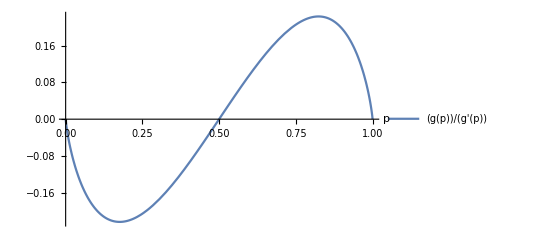

```mathematica
Framed[Plot[(p-1) p (Log[1-p]-Log[p]),{p,0,1},AxesLabel->{ToExpression["p",TeXForm,HoldForm]},PlotLegends->Placed[{ToExpression["g(p)/g'(p)",TeXForm,HoldForm]},{After,Top}]]]
```

Quadratic scoring rule

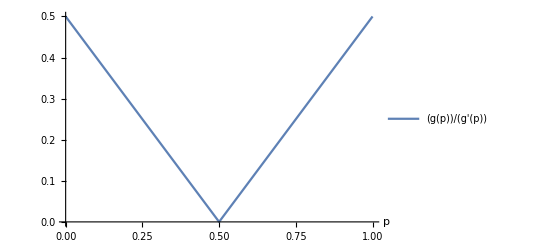

```mathematica
Framed[Plot[Abs[p-1/2],{p,0,1},AxesLabel->{ToExpression["p",TeXForm,HoldForm]},PlotLegends->Placed[{ToExpression["g(p)/g'(p)",TeXForm,HoldForm]},{After,Top}]]]
```

Indifference curves

Log scoring rule

```mathematica
IndifferenceTerm[probability_]:=Last@Last@Last@Solve[logscore[p,q]==logscore[probability,probability]]
```

```mathematica
f[p_]:=0.5*p+0.31
```

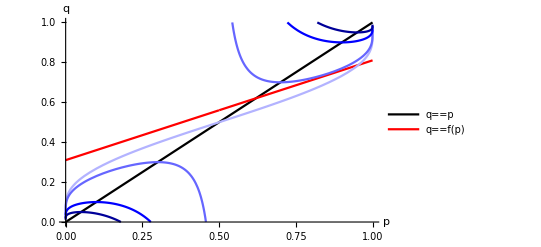

```mathematica
Framed[Plot[{p,f[p],IndifferenceTerm[1/2],IndifferenceTerm[7/10],
IndifferenceTerm[9/10],
IndifferenceTerm[95/100]},{p,0,1},PlotStyle->{Black,Red,Lighter[Blue,0.7],Lighter[Blue,0.4],Blue,Darker[Blue,0.4]},PlotRange->{{0,1},{0,1}},AxesLabel->{ToExpression["p",TeXForm,HoldForm],ToExpression["q",TeXForm,HoldForm]},Exclusions->p==1/2,PlotLegends->{ToExpression["q=p",TeXForm,HoldForm],ToExpression["q=f(p)",TeXForm,HoldForm]}]]
```

Exponential scoring rule

```mathematica
IndifferenceFunction[K_,p_,probability_]:=(ⅇ^(-K* p) (ⅇ^(probability*K)-ⅇ^(K p)+ⅇ^(K p) K p))/K
```

```mathematica
Manipulate[Plot[{p,IndifferenceFunction[K,p,1/10],IndifferenceFunction[K,p,3/10],IndifferenceFunction[K,p,1/2],IndifferenceFunction[K,p,7/10],IndifferenceFunction[K,p,9/10]},{p,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Black,Lighter[Blue,0.7],Lighter[Blue,0.35],Blue,Darker[Blue,0.35],Darker[Blue,0.7]},PlotLegends->{ToExpression["q=p",TeXForm,HoldForm]},AxesLabel->{ToExpression["p",TeXForm,HoldForm],ToExpression["q",TeXForm,HoldForm]}],{K,1,100}]
```

Inaccuracy as a function of the slope

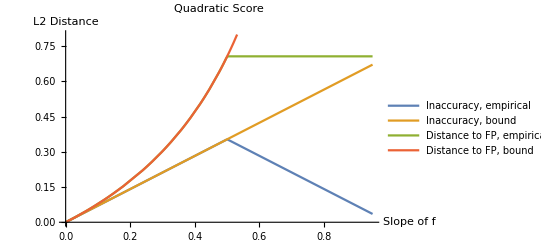

```mathematica
Plot[{ Sqrt[2]*MaxArgmaxScoreDistanceTof[slope,brierscore,L1Distance],BrierBoundf[slope],Sqrt[2]*MaxArgmaxScoreDistanceTofp[slope,brierscore,L1Distance],BrierBoundfp[slope]},{slope,0,0.95},PlotPoints->2,MaxRecursion->8,PlotLegends->{"Inaccuracy, empirical", "Inaccuracy, bound" , "Distance to FP, empirical" ,"Distance to FP, bound"},AxesLabel->{"Slope of f","L2 Distance"},PlotLabel->"Quadratic Score",PlotRange->{0,0.8}]
```

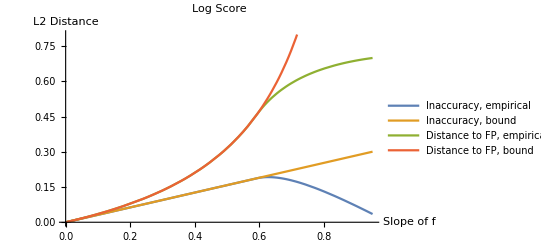

```mathematica
Plot[{NMaxArgmaxScoreDistanceTof[slope,logscore,L2DistanceVect],Boundf[slope,logscore],NMaxArgmaxScoreDistanceTofp[slope,logscore,L2DistanceVect],Boundfp[slope,logscore]},{slope,0,0.95},PlotPoints->2,MaxRecursion->7,PlotLegends->{"Inaccuracy, empirical", "Inaccuracy, bound" , "Distance to FP, empirical" ,"Distance to FP, bound"},AxesLabel->{"Slope of f","L2 Distance"},PlotLabel->"Log Score",PlotRange->{0,0.8}]
```

Redefining ArgmaxScore

For the following plots it works better to compute the ArgmaxScore as follows:

```mathematica
Clear[ArgmaxScore];
```

```mathematica
ArgmaxScore[fp_,slope_,S_]:=ArgmaxScore[fp,slope,S]=Last@Last@Last@NMaximize[{S[p,f[p,fp,slope]],{p>=0,p<=1}},{p},Method->{"RandomSearch"}]
```

Density plots

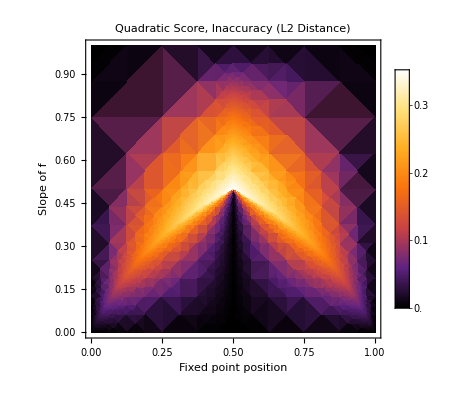

```mathematica
DensityPlot[ArgmaxScoreDistanceTof[fp,slope,brierscore,L2DistanceVect],{fp,0,1},{slope,0,1},PlotPoints->2,MaxRecursion->10,PlotLegends->Automatic,ColorFunction->ColorData["SunsetColors"],FrameLabel->{"Fixed point position","Slope of f"},PlotLabel->"Quadratic Score, Inaccuracy (L2 Distance)"]
```

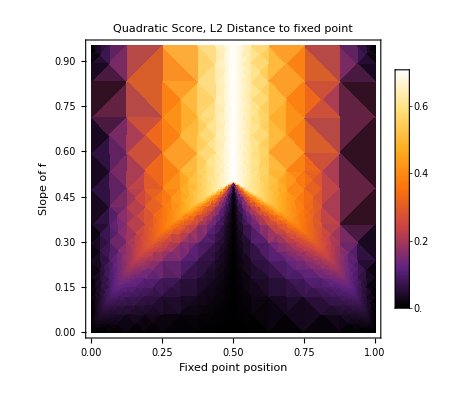

```mathematica
DensityPlot[ArgmaxScoreDistanceTofp[fp,slope,brierscore,L2DistanceVect],{fp,0,1},{slope,0,0.95},PlotPoints->2,MaxRecursion->10,PlotLegends->Automatic,ColorFunction->ColorData["SunsetColors"],FrameLabel->{"Fixed point position","Slope of f"},PlotLabel->"Quadratic Score, L2 Distance to fixed point"]
```

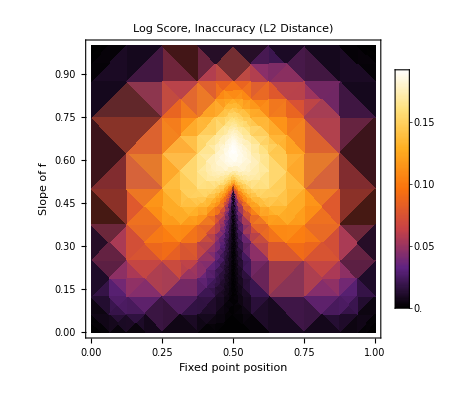

```mathematica
DensityPlot[ArgmaxScoreDistanceTof[fp,slope,logscore,L2DistanceVect],{fp,0,1},{slope,0,1},PlotPoints->2,MaxRecursion->9,PlotLegends->Automatic,ColorFunction->ColorData["SunsetColors"],FrameLabel->{"Fixed point position","Slope of f"},PlotLabel->"Log Score, Inaccuracy (L2 Distance)"]
```

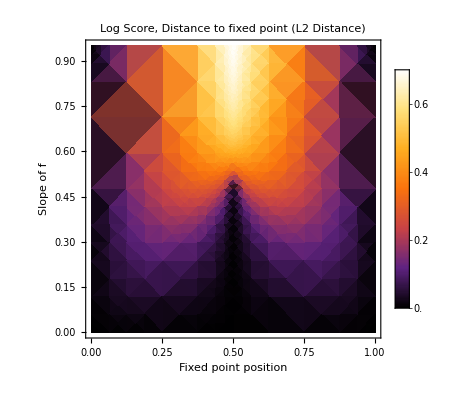

```mathematica
DensityPlot[ArgmaxScoreDistanceTofp[fp,slope,logscore,L2DistanceVect],{fp,0,1},{slope,0,0.95},PlotPoints->2,MaxRecursion->7,PlotLegends->Automatic,ColorFunction->ColorData["SunsetColors"],FrameLabel->{"Fixed point position","Slope of f"},PlotLabel->"Log Score, Distance to fixed point (L2 Distance)"]
```

Visualization`Core`DensityPlot::exclul: {Im[fp+slope (-fp+(SearchPoints→500))]-0,Im[-fp-slope (-fp+(SearchPoints→500))]-0} must be a list of equalities or real-valued functions.

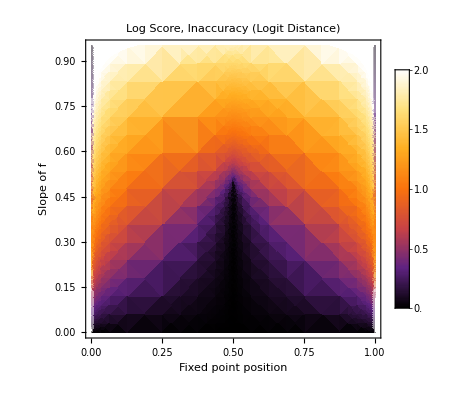

```mathematica
DensityPlot[ArgmaxScoreDistanceTof[fp,slope,logscore,AbsLogOddsRatio],{fp,0,1},{slope,0,0.95},PlotPoints->2,MaxRecursion->8,PlotLegends->Automatic,ColorFunction->ColorData["SunsetColors"],PlotRange->{0,2},FrameLabel->{"Fixed point position","Slope of f"},PlotLabel->"Log Score, Inaccuracy (Logit Distance)"]
```